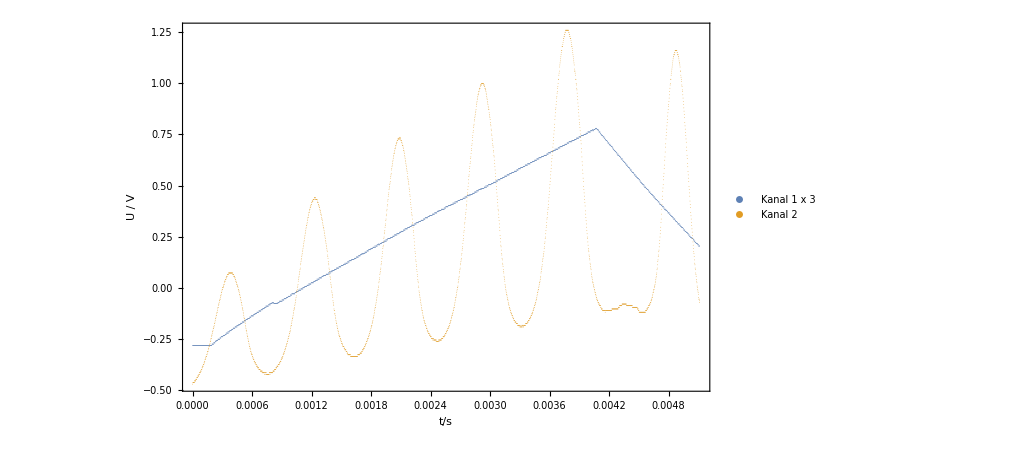

```mathematica
path = "./23-64.1mA-34.0C.tab";
ch1zoom = 3;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

```mathematica
Ramp={{0.004048,0.7689},{0.0009396,-0.05552}};
SlopeRamp=(Ramp[[1,2]]-Ramp[[2,2]])/(Ramp[[1,1]]-Ramp[[2,1]])(*V/s*)
SlopeRamp2=SlopeRamp*40*10^-3(*mA/ms*)
```

265.223

10.6089

{1.235,2.1,2.918,3.775}

{13.1869,17.3668,22.1939,26.2995,30.9569,35.2216,40.2078}

{0.,4.962,9.924,14.886,19.848,24.81,29.772}

| Estimate | Standard Error | t-Statistic | P-Value
a | -14.4195 | 0.288477 | -49.9851 | 6.05679×10^-8
b | 1.10627 | 0.0103147 | 107.251 | 1.33624×10^-9

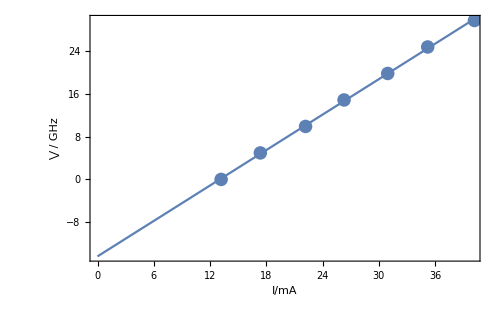

1.10627

```mathematica
Maxpos=Transpose[{{0.001235,0.4365},{0.0021,0.729},{0.002918,0.9905},{0.003775,1.261}}][[1]]1000
Maxpos=Transpose[{{0.001243,0.4365},{0.001637,-0.3348},{0.002092,0.7379},{0.002479,-0.2594},{0.002918,0.995},{0.00332,-0.1929},{0.00379,1.261}}][[1]]1000*SlopeRamp2
nus=Table[9.924i/2,{i,0,6}]
data=Transpose[{Maxpos,nus}];
nlm=NonlinearModelFit[data,a + b x,{a,b},x];
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{x,0,40},Frame->True,FrameLabel->{"I/mA","⋁ / GHz"},ImageSize->500],ListPlot[data]]
GHzmA=nlm["ParameterTableEntries"][[2,1]](*GHz/mA*)
```

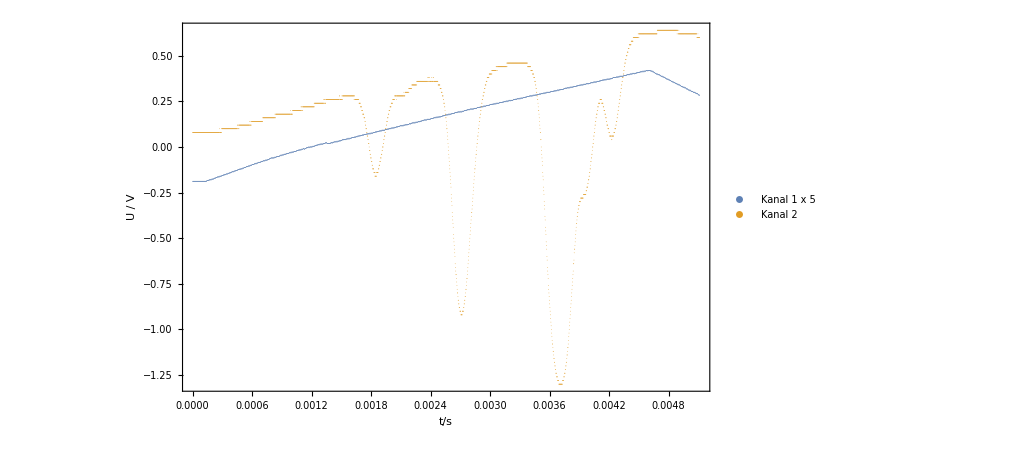

```mathematica
path = "./09-64.1mA-34.0C.tab";
ch1zoom = 5;
ch2zoom = 1;
SetDirectory[NotebookDirectory[]];
data = Drop[Import[path], 1];
ch1 = Transpose[{data[[All,1]],data[[All,2]]*ch1zoom}];
ch2 = Transpose[{data[[All,1]],data[[All,3]]*ch2zoom}];
ListPlot[{ch1, ch2}, PlotRange->All, Frame->True, ImageSize->750, PlotStyle->{PointSize[0.0001]}, PlotLegends->{"Kanal 1"<>If[ch1zoom ≠ 1, " x "<>ToString[ch1zoom], ""], "Kanal 2"<>If[ch2zoom ≠ 1, " x "<>ToString[ch2zoom], ""]}, FrameLabel->{"t/s", "U / V"}]
```

```mathematica
MinPos=Transpose[{{0.001849,-0.1533},{0.002115,0.2786},{0.002714,-0.9179},{0.003714,-1.3},{0.003942,-0.2725},{0.00423,0.0403}}][[1]]
```

{0.001849,0.002115,0.002714,0.003714,0.003942,0.00423}

```mathematica
Ramp2={{0.004533,0.4077},{0.001637,0.05519}};
SlopeRamp3=(Ramp2[[1,2]]-Ramp2[[2,2]])/(Ramp2[[1,1]]-Ramp2[[2,1]])(*V/s*)
SlopeRamp4=SlopeRamp3*40*10^-3(*mA/ms*)
```

121.723

4.86892

```mathematica
Measvals=MinPos*SlopeRamp4*GHzmA 1000
```

{9.97926,11.4149,14.6478,20.0449,21.2754,22.8298}

```mathematica
spectrum={-3.07,-2.25,Mean[{-1.48,-1.12}],Mean[{1.56,1.92}],3.76,4.58}
```

{-3.07,-2.25,-1.3,1.74,3.76,4.58}

FittedModel[-9.22549+0.587002 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | -9.22549 | 0.927757 | -9.94386 | 0.000574385
b | 1.70357 | 0.154591 | 11.0198 | 0.000385457

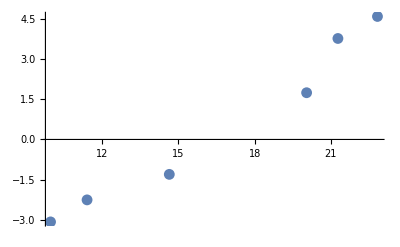

```mathematica
data=Transpose[{Measvals,spectrum}];
nlm=NonlinearModelFit[data,a+x/b,{a,b},x]
nlm["ParameterTable"]
ListPlot[data]
```